```mathematica
Integrate[Exp[-I n t],t]
```

(ⅈ ⅇ^(-ⅈ n t))/n

```mathematica
Integrate[Exp[-I n t],{t,0,2π}]
```

-(ⅈ (1-ⅇ^(-2 ⅈ n π)))/n

```mathematica
FullSimplify[ⅇ^(- ⅈ n π),Assumptions->n∈Integers]
```

(-1)^n

```mathematica
g[t_]:=π^2/6-1/2(t-π)^2
```

```mathematica
FullSimplify[Integrate[Exp[-I n t],{t,0,2π}],Assumptions->n ∈Integers]
```

-(2 π)/n^2

```mathematica
Integrate[-1/2 x^2 Exp[-I n (x+π)],{x,-π,π}]
```

-(ⅇ^(-ⅈ n π) (2 n π Cos[n π]+(-2+n^2 π^2) Sin[n π]))/n^3

```mathematica
f[x_]:=I x^2 Exp[-I n x]/n;
h[x_]:=2x Exp[-I n x]/n^2;
```

```mathematica
h[Pi]-h[-Pi]
```

(2 ⅇ^(-ⅈ n π) π)/n^2+(2 ⅇ^(ⅈ n π) π)/n^2

```mathematica
ExpToTrig[h[Pi]-h[-Pi]]
```

(4 π Cos[n π])/n^2

```mathematica
TeXForm@FullSimplify[ExpToTrig[h[Pi]-h[-Pi]],Assumptions->n∈Integers]
```

\frac{4 \pi  (-1)^n}{n^2}

```mathematica
(f[Pi]-f[-Pi])
```

(ⅈ ⅇ^(-ⅈ n π) π^2)/n-(ⅈ ⅇ^(ⅈ n π) π^2)/n

```mathematica
ExpToTrig[(ⅈ ⅇ^(-ⅈ n π) π^2)/n-(ⅈ ⅇ^(ⅈ n π) π^2)/n]
```

(2 π^2 Sin[n π])/n

```mathematica
FullSimplify[(2 π^2 Sin[n π])/n,Assumptions->n∈Integers]
```

0

```mathematica
Simplify[(ⅈ ⅇ^(-ⅈ n π) π^2)/n-(ⅈ ⅇ^(ⅈ n π) π^2)/n]
```

-(ⅈ ⅇ^(-ⅈ n π) (-1+ⅇ^(2 ⅈ n π)) π^2)/n

```mathematica
-2/n^2 Integrate[E^(-I n x),{x,-Pi,Pi}]
```

-(4 Sin[n π])/n^3

```mathematica
FourierCoefficient[g[t+π],t,n]
```

Piecewise[{{0, n==0}, {(-1)^(1+n)/n^2, True}}]

```mathematica
Integrate[]
```

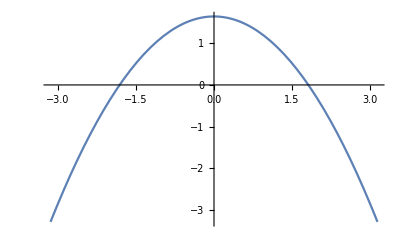

```mathematica
Plot[g[t+π],{t,-π,π}]
```

```mathematica
g[t-π]
```

π^2/6-1/2 (-2 π+t)^2

```mathematica
h[x_]:=2x Exp[-I n x]/n^2;
```

```mathematica
Integrate[x^2 Exp[-I n x],{x,-π,π}]//TrigToExp
```

(2 ((ⅇ^(-ⅈ n π)+ⅇ^(ⅈ n π)) n π+1/2 ⅈ (ⅇ^(-ⅈ n π)-ⅇ^(ⅈ n π)) (-2+n^2 π^2)))/n^3

```mathematica
Reduce[((2 ((ⅇ^(-ⅈ n π)+ⅇ^(ⅈ n π)) n π+1/2 ⅈ (ⅇ^(-ⅈ n π)-ⅇ^(ⅈ n π)) (-2+n^2 π^2)))/n^3)
==h[π]-h[-π]-(2 ⅈ ⅇ^(-ⅈ n π))/n^3+(2 ⅈ ⅇ^(ⅈ n π))/n^3+(2 ⅇ^(-ⅈ n π) π)/n^2+(2 ⅇ^(ⅈ n π) π)/n^2]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(2 ((ⅇ^(-ⅈ n π)+ⅇ^(ⅈ n π)) n π+1/2 ⅈ (ⅇ^(-ⅈ n π)-ⅇ^(ⅈ n π)) (-2+n^2 π^2)))/n^3==-(2 ⅈ ⅇ^(-ⅈ n π))/n^3+(2 ⅈ ⅇ^(ⅈ n π))/n^3+(4 ⅇ^(-ⅈ n π) π)/n^2+(4 ⅇ^(ⅈ n π) π)/n^2]

```mathematica
Integrate[x^2 Exp[-I n x],{x,-π,π}]//TrigToExp
```

(2 ((ⅇ^(-ⅈ n π)+ⅇ^(ⅈ n π)) n π+1/2 ⅈ (ⅇ^(-ⅈ n π)-ⅇ^(ⅈ n π)) (-2+n^2 π^2)))/n^3

```mathematica
-(2I)/n Integrate[x Exp[-I n x],{x,-Pi,Pi}]//TrigToExp
```

-(2 ⅈ ⅇ^(-ⅈ n π))/n^3+(2 ⅈ ⅇ^(ⅈ n π))/n^3+(2 ⅇ^(-ⅈ n π) π)/n^2+(2 ⅇ^(ⅈ n π) π)/n^2

```mathematica
FullSimplify[Exp[-I n π],Assumptions->n ∈Integers]
```

(-1)^n

```mathematica
j[x_]:=Exp[-I n x]((I x^2)/n+(2x)/n^2-(2i)/n^3)
```

```mathematica
j[π]-j[-π]
```

-ⅇ^(ⅈ n π) (-(2 i)/n^3-(2 π)/n^2+(ⅈ π^2)/n)+ⅇ^(-ⅈ n π) (-(2 i)/n^3+(2 π)/n^2+(ⅈ π^2)/n)

```mathematica
Simplify[j[π]-j[-π],Assumptions->n∈Integers]
```

```mathematica
(4 (-1)^n π)/n^2 G[t_]:=g[t-(Floor[t/(2π)](2π))]
```

```mathematica
E^(I π)
```

-1

```mathematica
FullSimplify[Integrate[(t-π)^2 Exp[-I n t],{t,0,2π}],Assumptions->n∈Integers]
```

(4 π)/n^2

```mathematica
G[t_]:=π^2/6-1/2(t-π)^2;
g[t_]:=G[t-(Floor[t/(2π)](2π))]
```

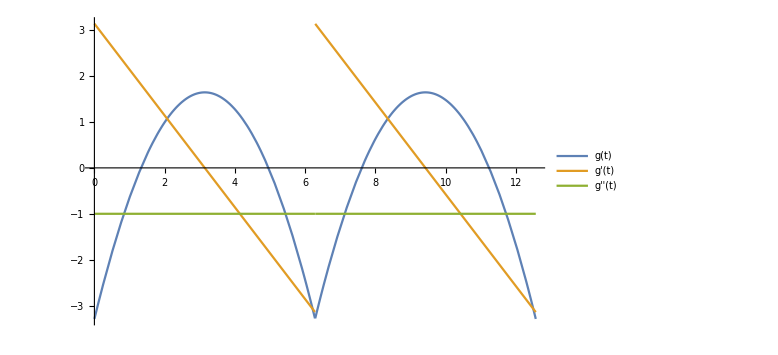

```mathematica
fig=Plot[{g[t],g'[t],g''[t]},{t,0,4π},AxesOrigin->{0,0},PlotLegends->"Expressions",ImageSize->Large]
```

```mathematica
Export["~/school/FA22/PHYS161a/figs/fourierplot.png",fig]
```

~/school/FA22/PHYS161a/figs/fourierplot.png

```mathematica
g''[t]
```

-(1-(Piecewise[{{0, t/(2 π)>Floor[t/(2 π)]}, {Indeterminate, True}}]))^2+(-π+t-2 π Floor[t/(2 π)]) (Piecewise[{{0, t-2 π Floor[t/(2 π)]>0}, {Indeterminate, True}}])

```mathematica
Sum
```

Problem 4

```mathematica
El[r_]:=E0 H[a-r]
```

```mathematica
1/r^2 D[r^2 El[r],r]
```

(2 E0 r H[a-r]-E0 r^2 H'[a-r])/r^2

```mathematica
Simplify[(2 E0 r H[a-r]-E0 r^2 H'[a-r])/r^2]
```

(2 E0 H[a-r])/r-E0 H'[a-r]

```mathematica
Integrate[2r H[a-r]-r^2 H'[a-r],r]
```

r^2 H[a-r]

```mathematica
∫_0^1 (2r H[a-r]-r^2 H'[a-r])ⅆr
```

∫_0^1 (2 r H[a-r]-r^2 H'[a-r])ⅆr

Problem 4

```mathematica
El[r_]:=E0 HeavisideTheta[a-r]
```

```mathematica
1/r^2 D[r^2 El[r],r]
```

(-E0 r^2 DiracDelta[a-r]+2 E0 r HeavisideTheta[a-r])/r^2

```mathematica
Cancel[(-E0 r^2 DiracDelta[a-r]+2 E0 r HeavisideTheta[a-r])/r^2//Apart]
```

-E0 DiracDelta[a-r]+(2 E0 HeavisideTheta[a-r])/r

```mathematica
Integrate[4π ϵ (D[r^2 El[r],r]),{r,0,Infinity}]
```

ConditionalExpression[0, a∈ℝ]

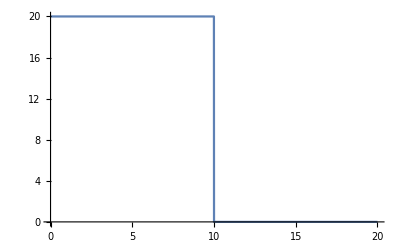

```mathematica
Plot[El[r]/.{a->10,E0->20},{r,0,20}]
```

```mathematica
Integrate[2r HeavisideTheta[a-r],{r,0,Infinity}]
```

ConditionalExpression[a^2 HeavisideTheta[a], a∈ℝ]

```mathematica
Integrate[r^2 DiracDelta[a-r],{r,0,Infinity}]
```

ConditionalExpression[a^2 HeavisideTheta[a], a∈ℝ]

```mathematica
FourierCoefficient[π^2/6-1/2 t^2,t,n]
```

Piecewise[{{0, n==0}, {(-1)^(1+n)/n^2, True}}]

```mathematica
Q[r_,a_]:=4Pi r^2 HeavisideTheta[a-r]
```

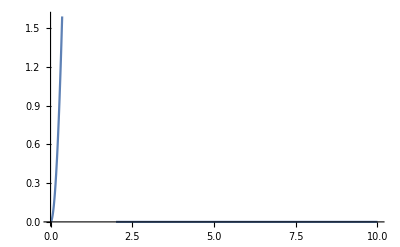

```mathematica
Plot[Q[r,2],{r,0,10}]
```

```mathematica
Integrate[E0 HeavisideTheta[a-r],{r}]
```

```mathematica
Limit[(ϵ/π)/(x^2+ϵ^2),ϵ->0]
```

0

```mathematica
Limit[Integrate[(ϵ/π)/((x-1)^2+ϵ^2)x^2,{x,-2,2}],ϵ->0]
```

Indeterminate

```mathematica
Integrate[DiracDelta[x]f[x],{x,-Infinity,Infinity}]
```

f[0]

```mathematica
delta[x_]:=(ϵ/π)/((x)^2+ϵ^2)
```

```mathematica
Limit[Apart[D[delta[x],x]],ϵ->0]
```

0

```mathematica
D[DiracDelta[x],x]
```

DiracDelta'[x]

```mathematica
D[delta[x],x]//Apart
```

-(2 x ϵ)/(π (x^2+ϵ^2)^2)

```mathematica
Integrate[(y x)/((y^2+x^2)^2),{x,-Infinity,Infinity}]
```

ConditionalExpression[0, Re[y]>0]

```mathematica
Series[Sinc[t],{t,0,10}]
```

1-t^2/6+t^4/120-t^6/5040+t^8/362880-t^10/39916800+O[t]^11

```mathematica
-Integrate[DiracDelta[t]D[Sin[a t]ϕ[t],t],{t,-Infinity,Infinity}]
```

-a ϕ[0]

```mathematica
-D[Sin[a t]ϕ[t],t]
```

-a Cos[a t] ϕ[t]-Sin[a t] ϕ'[t]

```mathematica
deltafunc[x_]:=Integrate
```

```mathematica
D[HeavisideTheta[t]*Sin[a t],{t,2}]
```

2 a Cos[a t] DiracDelta[t]-a^2 HeavisideTheta[t] Sin[a t]+Sin[a t] DiracDelta'[t]

```mathematica
Integrate[D[HeavisideTheta[t]Sin[a t],{t,2}]ϕ[t],{t,-Infinity,Infinity}]
```

$Aborted

```mathematica
D[HeavisideTheta[t]Sin[a t],{t,2}]
```

2 a Cos[a t] DiracDelta[t]-a^2 HeavisideTheta[t] Sin[a t]+Sin[a t] DiracDelta'[t]

```mathematica
f[t_]:=a^2 HeavisideTheta[t] Sin[a t]
```

```mathematica
f[t]/f[-t]
```

-HeavisideTheta[t]/HeavisideTheta[-t]

```mathematica
Integrate[HeavisideTheta[t]ϕ[t],{t,-Infinity,Infinity}]
```

∫_(-∞)^∞ HeavisideTheta[t] ϕ[t]ⅆt

```mathematica
TrigReduce[2Cos[a t]-1]
```

-1+2 Cos[a t]

```mathematica
D[G[t],
```

```mathematica
Manipulate[Plot[-1+2 Cos[a t],{t,-3.3856476981681354,3.385535088936411}],{a,-3.3856476981681283,3.3855350889364164}]
```

```mathematica
Integrate[(-1+2π Sum[DiracDelta[t-2 k π],{k,-Infinity,Infinity}])ϕ[t],{t,-Infinity,Infinity}]
```

∫_(-∞)^∞ (-1+DiracComb[t/(2 π)]) ϕ[t]ⅆt

```mathematica
2[Integrate[Sum[Cos[n x]ϕ[x],{n,0,Infinity}],{x,-Infinity,Infinity}]]
```

Sum::div: Sum does not converge.

2[∫_(-∞)^∞ (∑_(n=0)^∞ Cos[n x] ϕ[x])ⅆx]

```mathematica
FourierCosCoefficient[G[t],t,n]
```

-2/n^2